# Inlämningsuppgift #3: Matematisk modellering

Seema Bashir , TIDAB, sfbashir@kth.se
Esra Salman , TIDAB, esras@kth.se

Uppgift 1: Trafikflöde

## Sammanfattning

### Uppgift

Den här uppgiften går ut på och visa hur man kan använda linjära ekvationssystem för att studera trafikflödet genom ett trafiksystem. Trafiksystemet består av gator och korsningar där gatorna möts. Varje gata har ett visst flöde, som mäts i fordon per tidenhet. Vi ska beräkna trafikflödet för alla gatorna i trafiksystemet, givet flödet in till trafiksystemet. Vi gör ett viktigt antagande: Trafikflödet bevaras i varje korsning. Det betyder att ett fordon som når en korsning måste fortsätta genom trafiksystemet. Ett positivt värde på flödet flyter i pilens riktning och ett negativt flöde flyter i motsatt riktning.

Exempel (ej relaterat till figuren nedan):
Om flödet in till en fyrvägs korsning är y_1 fordon/tidsenhet respektive 30 fordon/tidsenhet och flödet ut från korsningen är y_2 fordon/tidsenhet respektive 50 fordon/tidsenhet, så gäller det att y_1+30=y_2+50  i korsningen. Efter förenkling får vi y_1-y_2=20. Varje korsning ger alltså en linjär ekvation i okända flöden y_1 och y_2. Om man löser ekvationssystemet så kan man bestämma flödet genom trafiksystemet.

a) Är vårt antagande om att flödet bevaras giltigt? 
b) När är antagandet felaktigt?
c) Vilka andra förenklingar har vi antagit?

Studera vägssystemet i figur 1. Siffrorna anger trafikflödena i fordon per timme. Alla vägar är enkelriktade och trafiken följer pilarnas riktning.

d) Ställ upp ekvationssystemet.
e) Bestäm trafikflödet för vägsystemet.
f) Om trafikflödet för en av vägarna x, y, z eller w≤ 100 fordon per timme på grund av vägarbete. Vad blir trafikflödet för de andra vägarna?

figur 1. Diagram av vägsystem i Kumasi, Ghana (efter Adu et al.[2014])

### Resultat

#### Uppgift a)

Påståendet “trafikflödet bevaras i varje korsning”, som innebär att mängden bilar som kommer in i korsning även går ut ur korsning (konstant),  är giltigt om Δtid är ∞ eller om bilinflödet stoppas samtidigt som bilar som redan befinner sig i systemet lämnar det.

#### Uppgift b)

Antagandet kan vara felaktigt då det finns bilar i systemet i olika tidslängder pga diverse anledningar som hastighet, då är inte in- och utflödet konstant under en godtycklig tidsperiod.

#### Uppgift c)

Antagandet är en förenkling av verkligheten då det finns fall där bilar som kommer in stannar kvar i systemet, som kan bero på att bilens slutdestination finns i trafiksystemet eller att bilen av andra orsaker fastnar.

#### Uppgift d)

```mathematica
w+z==516;
z+y==340;
x+y==255;
```

#### Uppgift e)

```mathematica
p=Reduce[{w+z==516, z+y==340, x+y==255}, {x,y,z,w}]
```

y==255-x&&z==85+x&&w==431-x

#### Uppgift f)

När z är högsta värdet 100 fordon/h:

```mathematica
z=100;
```

```mathematica
Reduce[p]
```

y==240&&x==15&&w==416

```mathematica
Clear[z]
```

När w är högsta värdet 100 fordon/h:

```mathematica
w= 100;
```

```mathematica
Reduce[p]
```

z==416&&y==-76&&x==331

```mathematica
Clear[z,w]
```

När x är högsta värdet 100 fordon/h:

```mathematica
x= 100;
```

```mathematica
Reduce[p]
```

y==155&&z==185&&w==331

```mathematica
Clear[z,w,x]
```

När y är högsta värdet 100 fordon/h:

```mathematica
y=100;
```

```mathematica
Reduce[p]
```

z==240&&x==155&&w==276

```mathematica
Clear[z,w,x,y]
```

Trafikflödet för samtliga vägar:

```mathematica
Reduce[p]
```

y==340-z&&x==-85+z&&w==516-z

## Kod

```mathematica
ClearAll["`*"]
```

Givna data införs

```mathematica
𝕙={0,2.6,5.1,6.3,4.3,2.6,1.3,1.7,2.8,1.5,0};
𝕩=Range[0,2000,200];
```

Tvärsnittsarean definieras som funktion av höjden

```mathematica
a0[h_]:=(10+2h)h
```

Data för a(x) tabelleras:

```mathematica
data=Transpose[{𝕩,a0[𝕙]}]
```

```mathematica
TableForm[Transpose[{𝕩,𝕙,a0[𝕙]}],TableHeadings->{None,{"x [m]","h [m]","a [m^2]"}}]
```

Funktionen a(x) kan nu interpoleras:

```mathematica
a=Interpolation[data]
```

```mathematica
Plot[a[x],{x,0,2000},AxesLabel->{x,A},AspectRatio->1/3]
```

Slutligen kan den efterfrågade volymen beräknas.

```mathematica
NIntegrate[a[x],{x,0,2000}]
```

Uppgift 2: Kaniner

## Sammanfattning

### Uppgift

Leonardo av Pisa, även känd som Fibonacci (circa 1170-1250) skapade en av de äldsta matematiska modellerna av förökning. Han modellerade förökning av kaniner. Genom att modellera kaninpar kunde han undvika att ta hänsyn till individuella kaniner av olika kön. Modellen beskriver förökningen av kaniner från månad n=1 där p_n är antal kaniner vid månad n. När en kanin föds, så är den en unge under en månad och sedan förökar sig kaninparen varje månad. Antal kaniner kan då beskrivs av en differensekvation:
p_(n+2)=p_(n+1)+p_n
där vi antar att vi har bara ett kaninpar vid månad n=1, dvs intialvärdena är p_1=1 och p_2=1. Vilket betyder att p_3=2,  p_4=3 och p_5=5..
a) Beräkna talföljden och rita en graf över den. Anpassa en lämplig funktion till punkterna och rita den i grafen.
b) Rita kurvan i en graf där y-axeln har logaritmisk skala.
c) Undersök talföljden och diskutera tillväxtakten, det vill säga tidsderivatan.
d) Exponentialfunktionen är lösning till differentialekvationen (d x)/(d t)=r x där r är tillväxt / populationsenhet, där vi antar att x är populationen. För att hantera att en viss plats bara kan ge mat till en viss mängd kaniner så kan man lägga till en korrektionsfaktor. Då får man logistiska tillväxtekvationen: (d x)/(d t)=r x [(K-x)/K]. När populationen närmar sig K så minskar populationsökningen till noll. Ekvationen kan lösas med hjälp av följande kommando:

```mathematica
DSolve[{x'[t]==r x[t](k-x[t])/k, x[0]==x0}, x[t], t]
```

Bortse från felmeddelandet. Tilldela resultatet ovan till en funktion (jämför hur ni använde Solve i förra inlämningsuppgiften). Bestäm värdet på x0 och r baserade på vad ni kom fram till i uppgift a) och b) . Rita sedan en graf över funktionen med Plot och använd sedan Manipulate för att variera värdet på k. 
Bestäm giltighetsområdet för Fibonaccis modell som funktion av värdet på K. Det vill säga vilket tidsintervall är modellen giltig för olika värden på K.

### Resultat

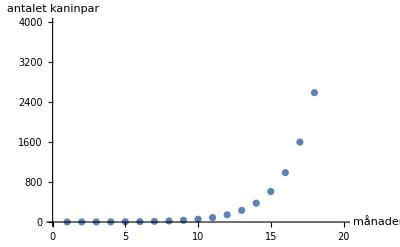
a)
Talföljd, upptill n=20:
{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765}

Funktion:
k[n_]:=k[n-2]+k[n-1]

Graf:
-Graphics-

b)

Graf:

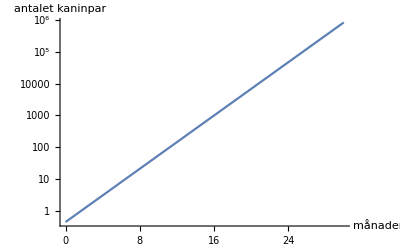

c)
Tillväxttakten: 0.215205 ⅇ^(0.481212 t)
Graf:

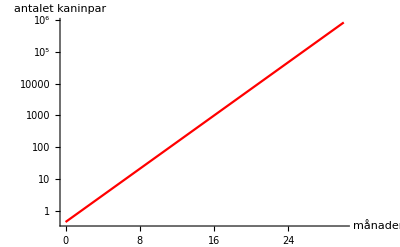

Diskussion: Tillväxttakten är konstant, det ser man i den räta linjen i grafen.

d)

Tidsintervall värdet på K är giltigt: 0 ≤ t ≤ 30 (t=tid i månader)

Graf:

## Kod

a)

Tilldelar en lämplig funktion:

```mathematica
k[1]=1;
k[2]=1;
k[n_]:=k[n-2]+k[n-1]
```

Beräkna talföljd:

```mathematica
kaninpar=Table[k[n],{n,1,20}]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765}

```mathematica
{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765}
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765}

Visualiserar graf:

```mathematica
Plot1=ListPlot[kaninpar,AxesLabel->{"månader", "antalet kaninpar"}]
```

-Graphics-

b)

Beräkna den exponetiella grafen:

```mathematica
{ak,bk}={a,b}/.FindFit[kaninpar,{a Exp[b t]},{a,b},t]
```

{0.447214,0.481212}

Inmata värden i graf, där y har logaritmisk skala:

```mathematica
totalt[t_]:=ak Exp[bk t]
```

```mathematica
plot2=LogPlot[totalt[t],{t,0,30},AxesLabel->{"månader","antalet kaninpar"}]
```

-Graphics-

Tillväxthastigheten ökar med tiden.

c) Tidsderivatan

Inmata resultat för graf till tidsderivatan:

```mathematica
LogPlot[totalt[t],{t,0,30},AxesLabel->{"månader","antalet kaninpar"},PlotStyle->Red]
```

-Graphics-

Beräkna tillväxttakten:

```mathematica
dekaninpar[t_]=D[totalt[t],t]
```

0.215205 ⅇ^(0.481212 t)

d)

```mathematica
{totaltK1[t_]}=x[t]/.DSolve[{x'[t]==r x[t](k-x[t])/k, x[0]==x0}, x[t], t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{(ⅇ^(r t) k x0)/(k-x0+ⅇ^(r t) x0)}

```mathematica
totaltK[t_]:=totaltK1[t]/.{x0->ak,r->bk}
```

Funktionen Manipulate används för variation på K - värdet, även Fibonaccis funktion och k ritas:

```mathematica
Manipulate[Plot[{totalt[t],k,{(ⅇ^(bk t) k ak)/(k-ak+ⅇ^(bk t) ak)}},{t,0,30}],{k,3000, 100000}]
```

## Diskussion

Fibonaccis modell gäller när k är mycket större än populationen. Därför är modellen endast giltig när det finns en större population, alltså där värdet på k är en hög värde. Om det finns en större population är även medelvärlden bättre och mätbart. I en population med t.ex 500 kanniner,  kan väder och omkringsvandrande predatorer avgöra att alla kaninener dör. Huruvida, i en population med t.ex 1000 kaniner, skulle inte vädret och andra omkringsvandrande predatorer orsaka att alla kaniner dör, utan en liten del av kaninen befolkningen skulle kunna dö. Därför finns det inte en påverka på modellen. Vidare kommer tidsderivaten för ökningen av antal kaniner att variera med tiden.  Tillväxthastigheten kommer att acceleras fram tills den uppnår en optimala tillväxthästigheten.